# Module 1a: Four-Vectors and Spacetime Diagrams

This notebook provides interactive visualizations of special relativity concepts. Each section builds on the Lorentz transformation formalism developed in lorentz_transforms.wl and the LaTeX notes.

## 1. The Minkowski Metric and Interval Classification

The spacetime interval ds^2 = -dt^2 + dx^2 + dy^2 + dz^2 classifies event separations as timelike (ds^2 < 0), null (ds^2 = 0), or spacelike (ds^2 > 0). We work in natural units c = 1.

```mathematica
(* Define the Minkowski metric *)
η = DiagonalMatrix[{-1, 1, 1, 1}]
MatrixForm[η]
```

{{-1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

Classify given event separations (cf. LaTeX Exercise 1.1):

```mathematica
(* Exercise: Classify event separations *)
(* Event pairs from the problem set *)
events = {
{{0,0,0,0}, {2,1,1,0}},
{{0,0,0,0}, {1,1,0,0}},
{{0,0,0,0}, {3,1,2,2}}};
classifyInterval[eventA_, eventB_] := Module[{dx, ds2},
dx = eventB - eventA;
ds2 = dx . η . dx;
Which[ds2 < 0, {ds2, "Timelike"},
ds2 == 0, {ds2, "Null"},
ds2 > 0, {ds2, "Spacelike"}]]
Table[{events[[i,2]], classifyInterval[events[[i,1]], events[[i,2]]]}, {i, 3}] // TableForm
```

2
1
1
0 | -2
Timelike
1
1
0
0 | 0
Null
3
1
2
2 | 0
Null

## 2. Spacetime Diagram with Light Cones

Interactive spacetime diagram showing the light cone structure. The light cone divides spacetime into timelike (inside), null (on the cone), and spacelike (outside) regions. Cf. Carroll Figures 1.2 and 1.5.

```mathematica
(* Spacetime diagram: 1+1 dimensions for clarity *)
(* Light cones are the lines x = +/- t *)
lightConePlot = Show[
(* Shade the timelike region *)
RegionPlot[x^2 < t^2, {x, -3, 3}, {t, -3, 3},
PlotStyle -> Directive[LightBlue, Opacity[0.3]],
BoundaryStyle -> None],
(* Light cone lines *)
Plot[{x, -x}, {x, -3, 3},
PlotStyle -> {{Orange, Dashed, Thick}, {Orange, Dashed, Thick}}],
(* Example worldlines *)
Graphics[{
(* Stationary particle: vertical worldline *)
{Blue, Thick, Arrow[{{0, -2.5}, {0, 2.5}}]},
(* Moving particle: v = 0.5 *)
{Red, Thick, Arrow[{{-0.5 * 2.5, -2.5}, {0.5 * 2.5, 2.5}}]},
(* Labels *)
{Text[Style["Timelike\n(inside cone)", 12, Blue], {0, 1.5}],
Text[Style["Spacelike\n(outside)", 12, Darker[Green]], {2.2, 0.5}],
Text[Style["Light cone\n(null)", 12, Orange], {2, 2.5}]}}],
AxesLabel -> {"x", "t"},
PlotLabel -> "Spacetime Diagram (1+1D)",
AspectRatio -> 1,
ImageSize -> 500];
lightConePlot
```

## 3. Interactive Lorentz Boost

Use the slider to vary the boost velocity v and see how the (t', x') axes tilt. Light cones (x = +/- t) are invariant under boosts. Cf. Carroll Figure 1.7.

```mathematica
(* Interactive Lorentz boost: see how the primed axes tilt *)
(* The t' axis is the line x = v*t; the x' axis is t = v*x *)
Manipulate[
Show[
(* Light cone *)
Plot[{x, -x}, {x, -3, 3},
PlotStyle -> {{Orange, Dashed}, {Orange, Dashed}}],
(* Primed axes *)
Graphics[{
(* t' axis: x = v*t, so t = x/v for display as x(t) *)
{Red, Thick, Arrow[{{0, 0}, {vBoost * 2.8, 2.8}}]},
(* x' axis: t = v*x *)
{Darker[Red], Thick, Arrow[{{0, 0}, {2.8, vBoost * 2.8}}]},
(* Labels *)
{Text[Style["t'", 14, Red, Bold], {vBoost*2.8 + 0.2, 2.9}],
Text[Style["x'", 14, Darker[Red], Bold], {2.9, vBoost*2.8 + 0.2}]}}],
AxesLabel -> {"x", "t"},
PlotRange -> {{-3, 3}, {-3, 3}},
AspectRatio -> 1,
PlotLabel -> Row[{"Lorentz Boost: v = ", NumberForm[vBoost, 2], ", γ = ", NumberForm[1/Sqrt[1 - vBoost^2], {4, 2}]}],
ImageSize -> 500],
{{vBoost, 0.3, "Velocity v/c"}, 0, 0.95, 0.01}]
```

## 4. Time Dilation Demonstration

The Lorentz factor gamma = 1/Sqrt[1 - v^2] determines how much a moving clock slows down relative to a stationary observer. This plot shows gamma as a function of v/c.

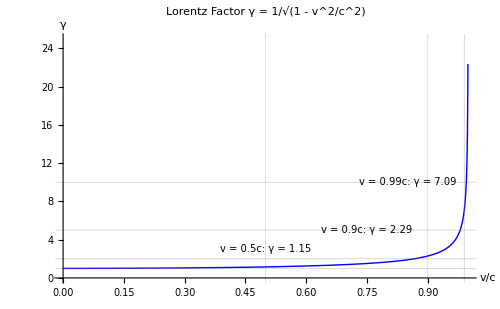

```mathematica
(* Plot the Lorentz factor gamma vs velocity *)
Plot[1/Sqrt[1 - v^2], {v, 0, 0.999},
PlotRange -> {0, 25},
AxesLabel -> {"v/c", "γ"},
PlotLabel -> "Lorentz Factor γ = 1/\!\(\*SqrtBox[\(1 - v\^2/c\^2\)]\)",
PlotStyle -> {Blue, Thick},
GridLines -> {{0.5, 0.9, 0.99}, {1, 2, 5, 10}},
Epilog -> {
Text[Style["v = 0.5c: γ = 1.15", 10], {0.5, 3}],
Text[Style["v = 0.9c: γ = 2.29", 10], {0.75, 5}],
Text[Style["v = 0.99c: γ = 7.09", 10], {0.85, 10}]},
ImageSize -> 500]
```

## 5. Twin Paradox (Carroll Fig. 1.6)

The traveling twin takes a longer path through space but a shorter path through spacetime (less proper time). This is the geometric origin of the twin paradox â.80.94 in Minkowski space, the straight path has the LONGEST proper time, opposite to Euclidean intuition.

```mathematica
(* Twin paradox: compare proper times along two paths *)
Manipulate[
Module[{totalT, halfT, xTurn, tauStay, tauTravel},
totalT = 4;
halfT = totalT/2;
xTurn = vTwin * halfT;
tauStay = totalT;
tauTravel = totalT * Sqrt[1 - vTwin^2];
Show[
Graphics[{
(* Stationary twin: straight worldline *)
{Blue, Thick, Arrow[{{0, 0}, {0, totalT}}]},
(* Traveling twin: bent worldline *)
{Red, Thick, Arrow[{{0, 0}, {xTurn, halfT}}],
Arrow[{{xTurn, halfT}, {0, totalT}}]},
(* Labels *)
{Text[Style[Row[{"Stay: τ = ", NumberForm[tauStay, 3]}], 12, Blue], {-1, 2}],
Text[Style[Row[{"Travel: τ = ", NumberForm[tauTravel, {4, 2}]}], 12, Red], {xTurn + 0.5, 2}]}}],
Axes -> True,
AxesLabel -> {"x", "t"},
PlotRange -> {{-2, 3}, {-0.5, 5}},
AspectRatio -> 1,
PlotLabel -> "Twin Paradox",
ImageSize -> 400]],
{{vTwin, 0.6, "Travel velocity v/c"}, 0.1, 0.95, 0.01}]
```

## 6. Index Manipulation with the Metric

Demonstrate raising and lowering indices using the Minkowski metric. V_mu = eta_{mu nu} V^nu flips the sign of the time component. (Carroll eqs. 1.72--1.75)

```mathematica
(* Example: lower the index of a four-vector *)
η = DiagonalMatrix[{-1, 1, 1, 1}];
Vup = {E0, px, py, pz};
Vdown = η . Vup;
Print["V^μ = ", Vup];
Print["V_μ = η_{μν} V^ν = ", Vdown];
Print["Note: V_0 = -V^0 (sign flip), V_i = V^i (no change)"];
(* Compute the invariant norm V^mu V_mu *)
norm = Vup . Vdown;
Print["V^μ V_μ = ", norm];
```

V^μ = {E0,px,py,pz}

V_μ = η_{μν} V^ν = {-E0,px,py,pz}

Note: V_0 = -V^0 (sign flip), V_i = V^i (no change)

V^μ V_μ = -E0^2+px^2+py^2+pz^2